```mathematica
mecca = {"Mecca",  "SaudiArabia"};
petra = {"Wadi Musa", "Jordan"};
jerusalem = {"Jerusalem", "Israel"};
```

```mathematica
direction[city_, qibla_] := GeoDirection@@(CityData[#, "Coordinates"]&/@{city,qibla})
```

```mathematica
compareQibla[city_, orientation_ : 0] := Module[
{a, o=Point@{0,0}, g={Red,Green,Blue,Gray}, l},
l=g~Riffle~{"Mecca","Petra","Jerusalem"};
a=Arrow@{{0,0},{Sin[#],Cos[#]}}&;
g=Riffle[g, a@direction[city,#]&/@{mecca,petra,jerusalem}];
If[orientation!=0,o=a[orientation];AppendTo[l,"Mosque Orientation"]];
g=Graphics[Flatten@Insert[{Thick,o,Dashed,Thin,Circle[]},g,2],
ImageSize->Medium,PlotLabel->ToString[city]~StringTrim~("{" | "}")];
Row@{g, LineLegend@@Transpose@Partition[l,2]}]
```

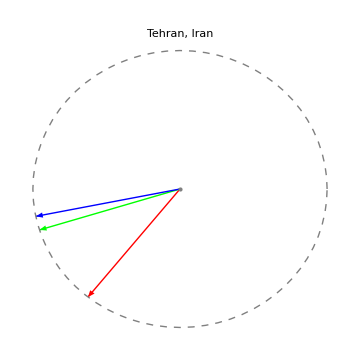

```mathematica
compareQibla[{"Tehran","Iran"}]
```

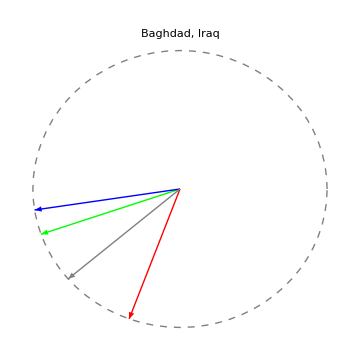

```mathematica
compareQibla[{"Baghdad","Iraq"},229.5°]
```